Graph Theory Homework 5

Load graph utilities because that’s what the homework said to do. I think we need some functions from that package.

```mathematica
<<GraphUtilities`
```

Load the graph data for the problem from the Mathematica server. Place them all in an array so that we can use “Table” to iterate over them.

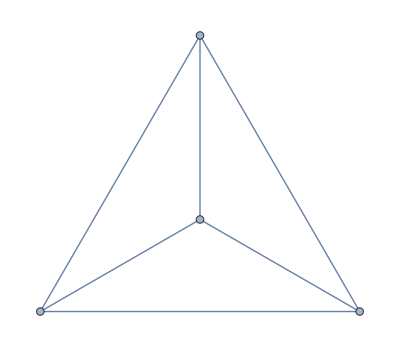
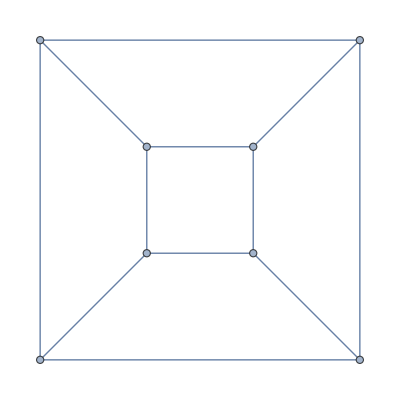
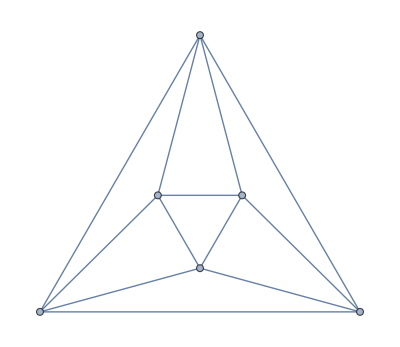
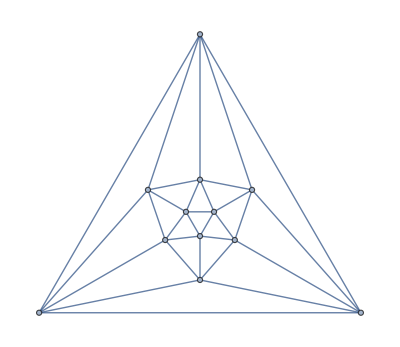
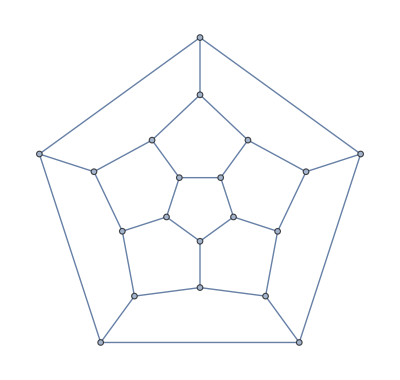

```mathematica
graphs = {
    GraphData["TetrahedralGraph"],
    GraphData["CubicalGraph"],
	GraphData["OctahedralGraph"],
	GraphData["IcosahedralGraph"],
	GraphData["DodecahedralGraph"]
}
```

Check this out. The Mathematica definition page for a Hamiltonian cycle had the answer to the problem.

Find and highlight Hamiltonian cycles.

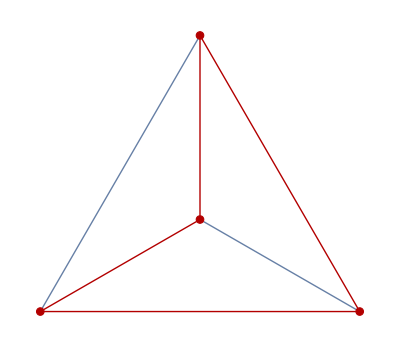
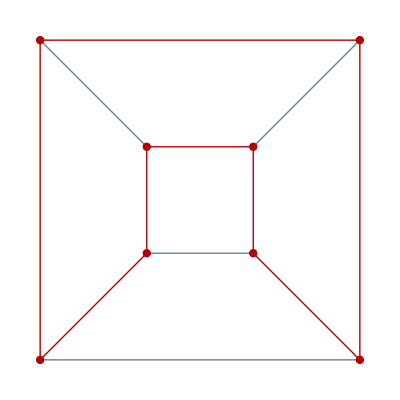
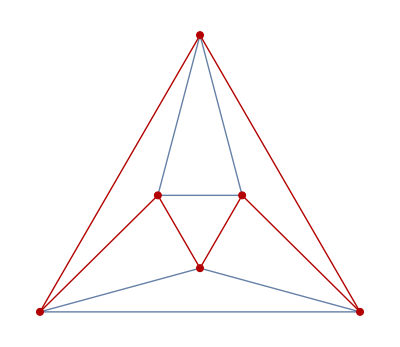
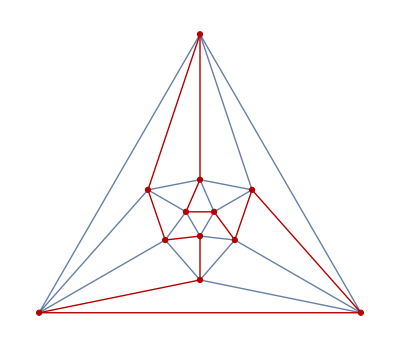
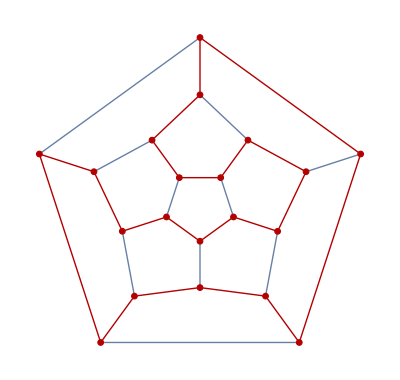

```mathematica
Table[HighlightGraph[i,PathGraph[First[FindHamiltonianCycle[i]]]],{i,graphs}]
```

Hamiltonian Path

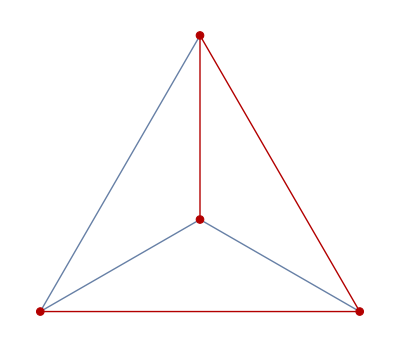
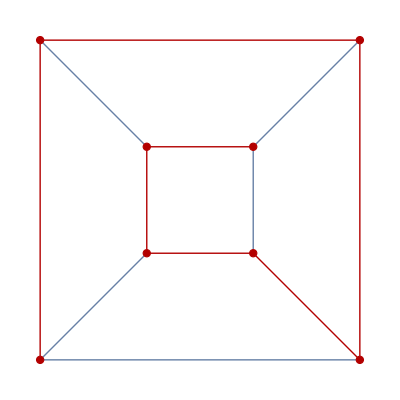
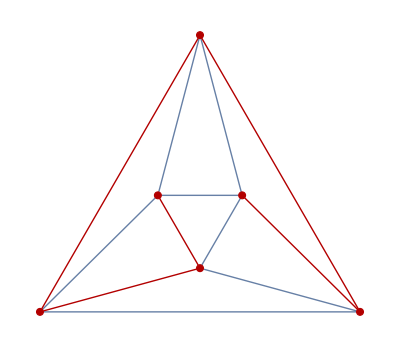
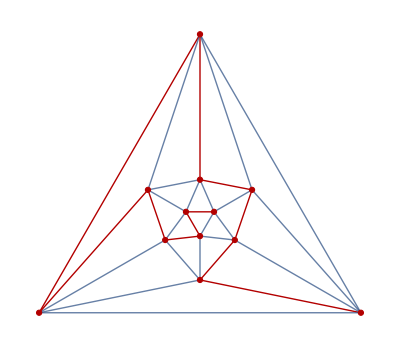
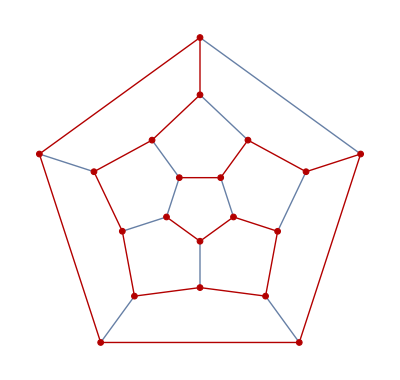

```mathematica
Table[HighlightGraph[i,PathGraph[FindHamiltonianPath[i]]],{i,graphs}]
```

Eulerian Cycle

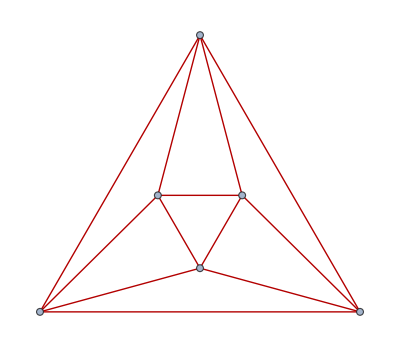
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[HighlightGraph[i,FindEulerianCycle[i]],{i,graphs}]
```